## Convert Covid-19 Cases

```mathematica
path0=NotebookDirectory[];
coviddata=Import[path0<>"covid.csv","CSV"];
days=DayCount[coviddata[[2,4]],coviddata[[-1,4]]]
cases=coviddata[[2;;,6]];
death=coviddata[[2;;,9]];
```

697

```mathematica
avgcase=Table[t1=Round[5.3*i];t2=Round[5.3*(i+1)];Round[Plus@@cases[[t1+1;;t2]]],{i,0,Floor[days/5.3]-1}];
avgdeath=Table[t1=Round[5.3*i];t2=Round[5.3*(i+1)];Round[Plus@@death[[t1+1;;t2]]],{i,0,Floor[days/5.3]-1}];
Export[path0<>"cases.csv",{avgcase},"CSV"];
Export[path0<>"casesD.csv",{avgdeath*1/0.0037},"CSV"];
```

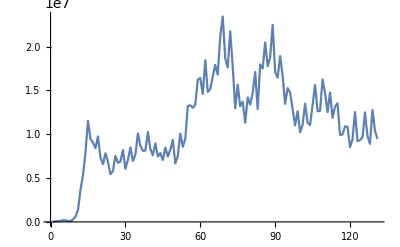

```mathematica
ListPlot[avgdeath*1/0.0037,Joined->True]
```

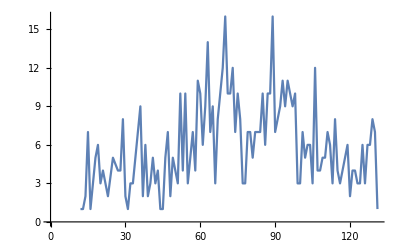

```mathematica
path0=NotebookDirectory[];
cases=Import[path0<>"casesD.csv","CSV"][[1]];
Table[{i,RandomVariate[BinomialDistribution[Floor@cases[[i]],5*10^-7],1][[1]]},{i,1,Length[cases]}];
data=Select[%,#[[2]]>0&];
ListPlot[data,Joined->True]
```

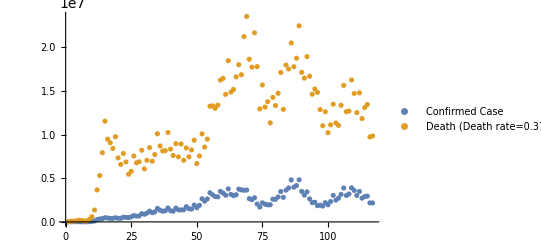

```mathematica
ListPlot[{avgcase,1/0.0037*avgdeath},PlotLegends->{"Confirmed Case","Death (Death rate=0.37%)"}]
```

```mathematica
(*Functions*)
TDeltaT[lineage_,n_]:=
Module[{t0},
t0=lineage[[1]];
{t0,lineage[[n+1]]}
]
getDeltaT[lineagelist_,n_]:=TDeltaT[#,n]&/@lineagelist

path0=NotebookDirectory[];
k = {1,2,3};
lineage=Import[path0<>"data/N2.0E+07K"<>ToString[#]<>"M1E-05A.out","CSV"]&/@k;
(*lineageA=Import[path0<>"data/K"<>ToString[#]<>"M5E-05A.out","CSV"]&/@k;*)
Mean/@lineage[[1;;3,;;,1]]//N(*T*)
Mean/@lineage[[1;;3,;;,2]]//N(*DeltaT*)
Dimensions/@lineage
```

{1.,23.334,109.923}

{4.163,4.716,7.148}

{{1000},{1000},{1000}}

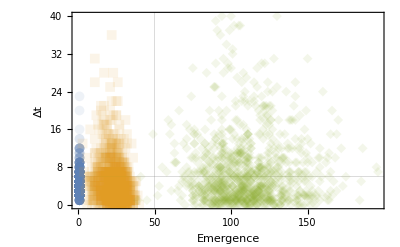

```mathematica
(*1st VOC: 2020Sep, 2nd VOC: 2020OCT*)
actual={{50,6}};

DataTDeltaT=getDeltaT[#,1]&/@lineage;
ListPlot[DataTDeltaT,PlotRange->All,PlotMarkers->{Automatic, Medium},Frame->True,FrameLabel->{"Emergence","Δt"},PlotStyle->Opacity[0.1],GridLines->{{{actual[[1,1]],{Thick,Red}}},{{actual[[1,2]],{Thick,Red}}}}]
```

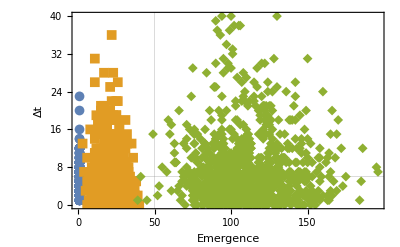

```mathematica
(*1st VOC: 2020Sep, 2nd VOC: 2020OCT*)
actual={{50,6}};

DataTDeltaT=getDeltaT[#,1]&/@lineage;
ListPlot[DataTDeltaT,PlotRange->All,PlotMarkers->{Automatic, Medium},Frame->True,FrameLabel->{"Emergence","Δt"},GridLines->{{{actual[[1,1]],{Thick,Red}}},{{actual[[1,2]],{Thick,Red}}}}]

Histogram3D[Append[DataTDeltaT,actual],Automatic,"Probability",ChartLabels->Placed[{"k=1","k=2","k=3","Real"},Above,"Framed"]]
```

## Dirichlet Multinomial Sampling

```mathematica
(*One genotype with n individuals*)
cond = {r->2,p->0.2,n->3,runs->10000};
distInd=NegativeBinomialDistribution[r,p]/.cond;
rand=RandomVariate[distInd,{runs,n}/.cond];
sumOfInd=Plus@@@rand;
distSum=NegativeBinomialDistribution[r*n,p]/.cond;
randSum=RandomVariate[distSum,runs/.cond];
```

```mathematica
Mean@sumOfInd//N
Mean@randSum//N
Variance@sumOfInd//N
Variance@randSum//N
```

24.1396

24.0297

123.33

119.547

```mathematica
(*2 genotypes with n_i individuals*)
cond = {rn1->2,p1->0.2,rn2->3,p2->0.1,runs->1000};
dist1=NegativeBinomialDistribution[rn1,p1]/.cond;
dist2=NegativeBinomialDistribution[rn2,p2]/.cond;
n1=RandomVariate[dist1,runs/.cond];
n2=RandomVariate[dist2,runs/.cond];
nTot=n1+n2;
```

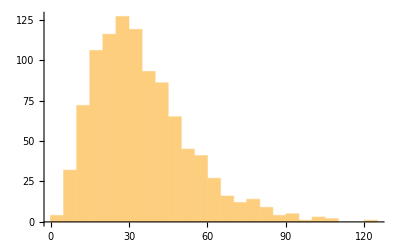

```mathematica
Histogram[nTot]
```

## Scalar in DM

```mathematica
Clear[k]
Solve[Ntt/Nt*(Ntt+A)/(1+A)==R(1+R/k)//.{R->Ntt/Nt},A]
Simplify[A/.%]
```

{{A→(-k Nt-Ntt+k Nt Ntt)/Ntt}}

{-1+(k Nt (-1+Ntt))/Ntt}

```mathematica
path0=NotebookDirectory[];
cases=Import[path0<>"casesD.csv","CSV"][[1]];
```

```mathematica
R=Table[cases[[i+1]]/cases[[i]],{i,1,Length[cases]-1}]
```

{4.30769,1.275,1.11765,1.8797,0.802667,0.669435,0.947891,2.65969,2.17717,2.27622,2.68937,1.44827,1.49442,1.45515,0.821343,0.956519,0.927531,1.16106,0.75131,0.898296,1.18997,0.875108,0.795331,1.06094,1.30369,0.89568,1.01961,1.19113,0.739191,1.16398,1.20542,0.815894,1.10948,1.31182,0.858286,0.935651,1.0033,1.25932,0.811541,0.91372,1.17957,0.831454,1.0549,0.896837,1.20269,0.877872,1.10717,1.13464,0.713464,1.13347,1.33292,0.85005,1.10648,1.39547,1.00494,0.978515,1.02783,1.21327,1.01264,0.888161,1.26473,0.803714,1.02181,1.09392,1.0801,0.938894,1.25884,1.10733,0.795507,0.945338,1.23382,0.815661,0.73009,1.20955,0.841871,1.04005,0.825865,1.25459,0.942089,1.09726,1.16422,0.752102,1.3968,0.973961,1.17049,0.867086,1.05653,1.19779,0.762025,0.961038,1.14926,0.88137,0.807726,1.13336,0.968692,0.870576,0.85522,1.14732,0.809091,1.08427,1.21781,0.839573,0.975569,1.20501,1.1735,0.807513,1.00439,1.28243,0.904443,0.85256,1.17753,0.804955,1.10685,1.02869,0.733566,1.00466,1.09326,0.995685,0.785988,1.10485,1.33122,0.735528,1.01128,1.03345,1.29528,0.783716,0.910494,1.43379,0.81345,0.910488}